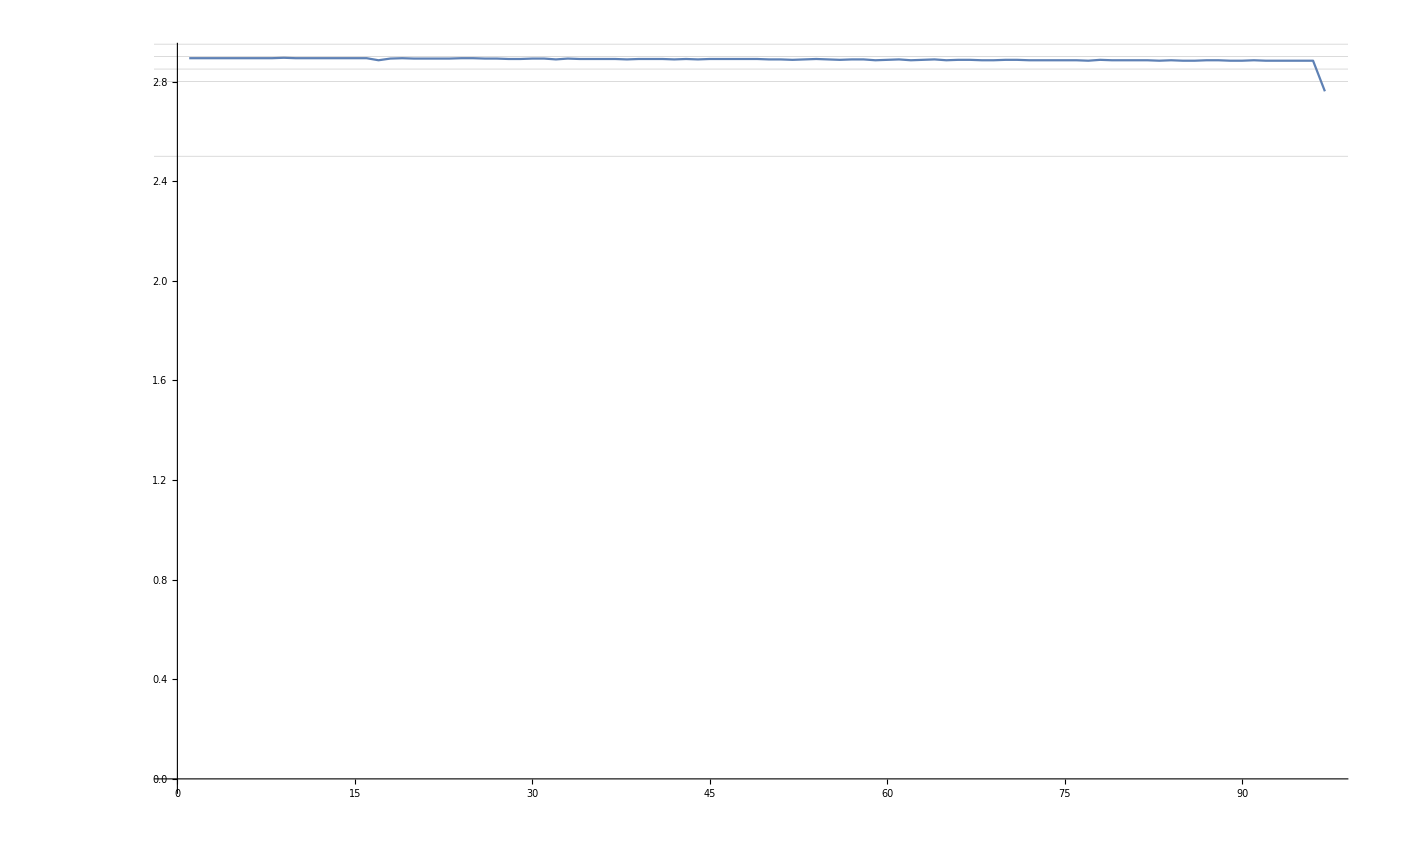

```mathematica
ListLinePlot[ToExpression[StringSplit[NotebookGet[ClipboardNotebook[]][[1,1,1]],","]],AxesOrigin->{0,0.0},GridLines->{{},{2.5,2.8,2.85,2.9,2.95,3.0}}]
```

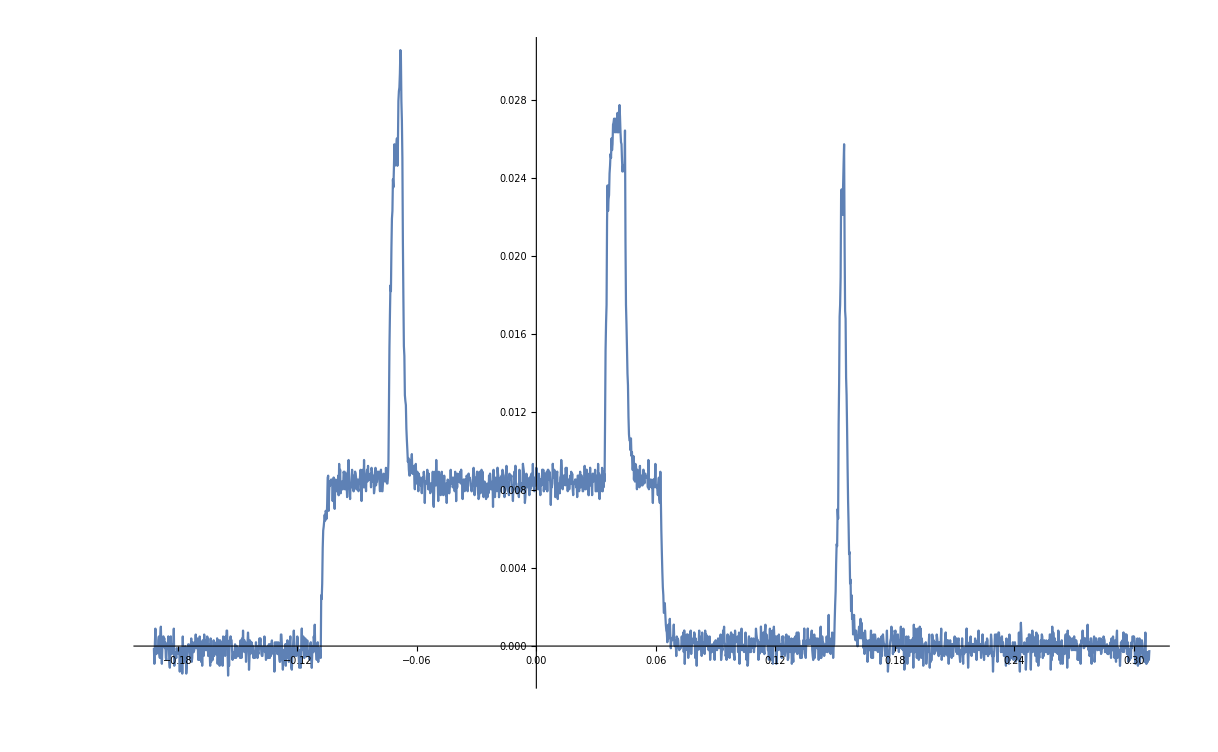

```mathematica
time=Import["/Users/jiahao/Desktop/scope_0.csv", "Data"][[3;;,1]];
voltages=Import["/Users/jiahao/Desktop/scope_0.csv", "Data"][[3;;,2]];
smooth=1;
ListLinePlot[Transpose[{time[[smooth;;]], MovingAverage[voltages+0.002,smooth]}],AxesOrigin->{0,0}]
```